# Clear console

```mathematica
Quiet@Remove["Global`*"]
SetDirectory[NotebookDirectory[]];
```

# Parameters

```mathematica
nmax=155;
var={u,v};
par={α,c,δ};
nvar=Length[var];
fixedpar={δ->0.6055300708194983};
parval={α->1/16*(21+√313),c->(1/16*(21+√313)+1)^2+1}//N;
ηval={ηNF->-0.0919995105221395}//N;
ξval={ξNF->-0.801397527511603}//N;
κval={κNF^2->ⅈ/kNF}//N;
C11eval={C11->0.0906146798703153*ⅈ}//N;
```

# Equation

```mathematica
kinetics={α/δ-c*u+u^2*v,(c-1)*u-u^2*v};
diffmatrix=DiagonalMatrix[{δ^2,1}];
eq=Solve[kinetics==0,var][[1]];
jacmat=D[kinetics,{var}]/.eq;
kinetics=kinetics/.Table[var[[varnum]]->var[[varnum]]+(var[[varnum]]/.eq),{varnum,nvar}];
```

# Kernel of the Jacobian matrix

```mathematica
dummymat=Table[Subscript[dmat, row,col],{row,nvar},{col,nvar}];
dummyvec=Table[Subscript[dvec, varnum],{varnum,nvar}];
jacobianmat=jacmat-μNF*diffmatrix/.fixedpar;
Tcond2=D[Det[jacobianmat],μNF];
μval=Solve[Tcond2==0,μNF][[1]]/.parval;
AppendTo[μval,kNF->(√μNF/.μval)];
κval=κval/.μval;
AppendTo[parval,μNF->kNF^2];
jacobianmat=jacobianmat;
ϕNF=Table[Subscript[vNF, varnum],{varnum,nvar}];
getout=0;
For[row=1,row<=nvar,row++,
If[getout==1,
Break[]];
For[col=1,col<=nvar,col++,
submatrixrows=Complement[Range[nvar],{row}];
submatrixcols=Complement[Range[nvar],{col}];
If[Det[jacobianmat[[submatrixrows,submatrixcols]]/.μval/.parval]!=0,
criticalrow=row;
criticalcol=col;
getout=1;
Break[];
]
];
]
ϕNF[[criticalcol]]=1;
ϕsol=Solve[Dot[jacobianmat[[submatrixrows,submatrixcols]],ϕNF[[submatrixcols]]]==-jacobianmat[[submatrixrows,{criticalcol}]],ϕNF[[submatrixcols]]][[1]];
ϕNF=ϕNF/.ϕsol;
Subscript[sol, 1,1]=Table[Subscript[WNF, 1,1,varnum]->C11*ϕNF[[varnum]],{varnum,nvar}];
```

# Kernel of the adjoint

```mathematica
ψNF=Table[Subscript[vNF, varnum],{varnum,nvar}];
ψNF[[criticalrow]]=1;
ψsol=Solve[Dot[Transpose[jacobianmat[[submatrixrows,submatrixcols]]],ψNF[[submatrixrows]]]==-Transpose[jacobianmat[[{criticalrow},submatrixcols]]],ψNF[[submatrixrows]]][[1]];
ψNF=ψNF/.ψsol/.fixedpar;
```

# Variables to expand

```mathematica
jacobianmat=jacobianmat/.parval;
jacobianmatr=jacmat-rNF^2*μNF*diffmatrix/.parval/.fixedpar;
ϕNF=ϕNF/.μval/.parval/.C11eval;
ψNF=ψNF/.μval/.parval;
Subscript[sol, 1,1]=Subscript[sol, 1,1]/.μval/.parval/.C11eval;
negativetab=Table[ⅇ^(ⅈ*subsub*kNF*x)->0,{subsub,-nmax,-1}];
positivetab=Table[ⅇ^(ⅈ*subsub*kNF*x)->0,{subsub,1,nmax}];
solr1=LinearSolve[dummymat[[submatrixrows,submatrixcols]],dummyvec[[submatrixcols]]];
solrn1=LinearSolve[dummymat,dummyvec];
toexpand=Flatten[Table[Subscript[var⟦varnum⟧, order]->Sum[Subscript[WNF, order,sub,varnum] ⅇ^(ⅈ sub kNF x)/.Subscript[WNF, order,sub,varnum]->If[sub<0,(-1)^order*ⅇ^(2*sub*ξNF*π)*Conjugate[Subscript[WNF, order,-sub,varnum]]/.ξval,Subscript[WNF, order,sub,varnum]],{sub,-order,order,2}],{order,nmax},{varnum,nvar}]];
toexpand=toexpand/. Subscript[sol, 1,1];
expr=kinetics/.Table[var[[varnum]]->∑_(order=1)^nmax ϵNF^order*Subscript[var[[varnum]], order],{varnum,nvar}]/.parval/.fixedpar;
derivative=D[expr,ϵNF];
```

# Iterative solver

```mathematica
load=1;
SetDirectory[NotebookDirectory[]];
If[FileExistsQ["savedSession.mx"] && load==1,
<<savedSession.mx
,
solvcond={};
ampeval={};
AppendTo[solvcond,0];
]
For[order=If[solvcond=={},2,Length[solvcond]+1],order<=nmax,order++,
save=0;
Print["order="<>ToString[order]];
derivative=D[derivative,ϵNF];
toexpand=toexpand/.ampeval;
equation=1/(order!)*derivative/.ϵNF->0/.toexpand;
equation=Expand[equation]/.negativetab;
If[OddQ[order],
sub=1;
auxeq=Chop[kNF/(2π)∫_0^((2π)/kNF) equation*ⅇ^(-ⅈ*sub*kNF*x)ⅆx];
auxeq=-(auxeq-Dot[jacobianmatr/.rNF->0,Table[Subscript[WNF, order,sub,varnum],{varnum,nvar}]])//Simplify;
If[order>=3,
If[order-2>=sub && OddQ[order],
auxeq=auxeq-2*ⅈ*sub*kNF*(order-2-2*ⅈ*sub*ηNF)/2*Dot[diffmatrix,Table[Subscript[WNF, order-2,sub,varnum],{varnum,nvar}]]/. Subscript[sol, order-2,sub]/.ηval;
]
];
If[order>=5,
If[order-4>=sub && OddQ[order],
auxeq=auxeq-((order-2-2*ⅈ*sub*ηNF)*(order-4-2*ⅈ*sub*ηNF))/4*Dot[diffmatrix,Table[Subscript[WNF, order-4,sub,varnum],{varnum,nvar}]]/. Subscript[sol, order-4,sub]/.ηval;
]
];
auxeq=auxeq/.fixedpar/.ampeval;
AppendTo[solvcond,Chop[Simplify[Dot[auxeq,ψNF]/.μval/.fixedpar]]];
If[order>=7 && OddQ[order],
If[order==7,
partialsol={Subscript[ANF, 3]->0.0726177257073768+0.00611449121220123*ⅈ};
,
actualeq=solvcond[[order]];
partialsol=Quiet@NSolve[actualeq==0,Subscript[ANF, order-4],Complexes][[1]];
];
ampeval=Join[ampeval,partialsol];
];
auxeq=auxeq/.ampeval;
usefulvec=Table[Subscript[auxvec, order,sub,varnum],{varnum,nvar}];
auxsol=solr1/.Flatten[Table[dummymat[[row,col]]->jacobianmat[[row,col]],{row,nvar},{col,nvar}]]/.Table[dummyvec[[varnum]]->auxeq[[varnum]],{varnum,nvar}];
usefulvec[[submatrixcols]]=Table[Subscript[WNF, order,sub,submatrixcols[[varnum]]]->auxsol[[varnum]]+Subscript[ANF, order]*ϕNF[[submatrixcols[[varnum]]]],{varnum,nvar-1}];
usefulvec[[criticalcol]]=Subscript[WNF, order,sub,criticalcol]->Subscript[ANF, order]*ϕNF[[criticalcol]];
Subscript[sol, order,sub]=Chop[usefulvec]/.μval/.C11eval//Expand;
toexpand=toexpand/. Subscript[sol, order,sub];
,
AppendTo[solvcond,0];
];
For[sub=If[EvenQ[order],0,3],sub<=order,sub+=2,
save=1;
If[sub==0,
auxeq=equation/.positivetab;
,
auxeq=equation/.ⅇ^(ⅈ*sub*kNF*x)->1/.positivetab;
];
auxeq=-(auxeq-Dot[jacobianmatr/.rNF->0,Table[Subscript[WNF, order,sub,varnum],{varnum,nvar}]])//Simplify;
If[order>=3,
If[order-2>=Abs[sub] && ((OddQ[order] && OddQ[sub]) || (EvenQ[order] && EvenQ[sub])),
auxeq=auxeq-2*ⅈ*sub*kNF*(order-2-2*ⅈ*sub*ηNF)/2*Dot[diffmatrix,Table[Subscript[WNF, order-2,sub,varnum],{varnum,nvar}]]/. Subscript[sol, order-2,sub]/.ηval;
]
];
If[order>=5,
If[order-4>=Abs[sub] && ((OddQ[order] && OddQ[sub]) || (EvenQ[order] && EvenQ[sub])),
auxeq=auxeq-((order-2-2*ⅈ*sub*ηNF)*(order-4-2*ⅈ*sub*ηNF))/4*Dot[diffmatrix,Table[Subscript[WNF, order-4,sub,varnum],{varnum,nvar}]]/. Subscript[sol, order-4,sub]/.ηval;
]
];
auxeq=auxeq/.fixedpar/.ampeval;
auxsol=solrn1/.Flatten[Table[dummymat[[row,col]]->jacobianmatr[[row,col]]/.rNF->sub,{row,nvar},{col,nvar}]]/.Table[dummyvec[[varnum]]->auxeq[[varnum]],{varnum,nvar}]/.μval/.C11eval;
Subscript[sol, order,sub]=Chop[Table[Subscript[WNF, order,sub,varnum]->auxsol[[varnum]],{varnum,nvar}]]/.ampeval//Expand;
toexpand=toexpand/. Subscript[sol, order,sub];
If[sub==0,
equation=equation-(Expand[equation]/.positivetab);
]
];
If[save==1 && sub==order+2,
DumpSave["savedSession.mx",{"Global`","Subscript"}]
]
]
```

order=2

order=3

order=4

order=5

order=6

order=7

order=8

order=9

order=10

order=11

order=12

order=13

order=14

order=15

order=16

order=17

order=18

order=19

order=20

order=21

order=22

order=23

order=24

order=25

order=26

order=27

order=28

order=29

order=30

order=31

order=32

order=33

order=34

order=35

order=36

order=37

order=38

order=39

order=40

order=41

order=42

order=43

order=44

order=45

order=46

order=47

order=48

order=49

order=50

order=51

order=52

order=53

order=54

order=55

order=56

order=57

order=58

order=59

order=60

order=61

order=62

order=63

order=64

order=65

order=66

order=67

order=68

order=69

order=70

order=71

order=72

order=73

order=74

order=75

order=76

order=77

order=78

order=79

order=80

order=81

order=82

order=83

order=84

order=85

order=86

order=87

order=88

order=89

order=90

order=91

order=92

order=93

order=94

order=95

order=96

order=97

order=98

order=99

order=100

order=101

order=102

order=103

order=104

order=105

order=106

order=107

order=108

order=109

order=110

order=111

order=112

order=113

order=114

order=115

order=116

order=117

order=118

order=119

order=120

order=121

order=122

order=123

order=124

order=125

order=126

order=127

order=128

order=129

order=130

order=131

order=132

order=133

order=134

order=135

order=136

order=137

order=138

order=139

order=140

order=141

order=142

order=143

order=144

order=145

order=146

order=147

order=148

order=149

order=150

order=151

order=152

order=153

order=154

order=155

# Tabulating information

```mathematica
SetDirectory[NotebookDirectory[]];
<<savedSession.mx
PrependTo[ampeval,Subscript[ANF, 1]->C11/.C11eval];
c00tabaux=Table[1/Dot[ϕNF,ϕNF]*((κNF^2/.κval)^(-(order-1)/2)*Dot[Table[Subscript[WNF, order,0,varnum],{varnum,nvar}]/. Subscript[sol, order,0],ϕNF]/.ampeval)/Gamma[(order-1)/2+3-ηNF*ⅈ]/.ηval/.C11eval,{order,2,Length[solvcond]-4,2}];
c20tabaux=Table[1/Dot[ϕNF,ϕNF]*((κNF^2/.κval)^(-(order-1)/2)*Dot[Table[Subscript[WNF, order,2,varnum],{varnum,nvar}]/. Subscript[sol, order,2],ϕNF]/.ampeval)/Gamma[(order-1)/2+3-ηNF*ⅈ]/.ηval/.C11eval,{order,2,Length[solvcond]-4,2}];
c00tab=Table[{Abs[c00tabaux[[ind]]],Arg[c00tabaux[[ind]]]},{ind,Length[c00tabaux]}];
c00tab[[All,1]]
c20tab=Table[{Abs[c20tabaux[[ind]]],Arg[c20tabaux[[ind]]]},{ind,Length[c20tabaux]}];
c20tab[[All,1]]
```

{0.0379125,0.0150264,0.0631502,0.0702186,0.0627784,0.106782,0.108977,0.115413,0.126165,0.118584,0.132142,0.120182,0.133735,0.121265,0.133371,0.122164,0.132056,0.122981,0.130275,0.123741,0.128286,0.124448,0.126231,0.125104,0.124189,0.12571,0.122201,0.126269,0.120289,0.126784,0.118462,0.127259,0.116724,0.127699,0.115072,0.128107,0.113504,0.128485,0.112015,0.128838,0.110601,0.129168,0.109256,0.129476,0.107976,0.129766,0.106757,0.130038,0.105594,0.130295,0.104484,0.130538,0.103422,0.130768,0.102406,0.130986,0.101433,0.131194,0.100499,0.131392,0.0996014,0.13158,0.0987389,0.131761,0.0979088,0.131933,0.0971092,0.132099,0.0963381,0.132257,0.095594,0.13241,0.0948752,0.132557,0.0941803}

{0.000843491,0.000465052,0.000497914,0.000504382,0.000449778,0.000420626,0.000422546,0.00039594,0.000405928,0.000388681,0.0003988,0.000386762,0.000395913,0.000386897,0.000395097,0.000387986,0.000395384,0.000389563,0.000396295,0.000391399,0.000397572,0.000393368,0.000399064,0.00039539,0.000400674,0.000397418,0.00040234,0.00039942,0.000404022,0.000401375,0.000405692,0.000403273,0.000407334,0.000405106,0.000408935,0.000406869,0.000410489,0.000408563,0.000411992,0.000410187,0.000413443,0.000411744,0.00041484,0.000413234,0.000416184,0.000414662,0.000417476,0.000416029,0.000418719,0.000417338,0.000419913,0.000418593,0.000421061,0.000419797,0.000422165,0.000420951,0.000423226,0.000422059,0.000424247,0.000423122,0.00042523,0.000424145,0.000426177,0.000425128,0.000427088,0.000426074,0.000427967,0.000426984,0.000428815,0.000427862,0.000429633,0.000428707,0.000430422,0.000429523,0.000431185}

# Plotting

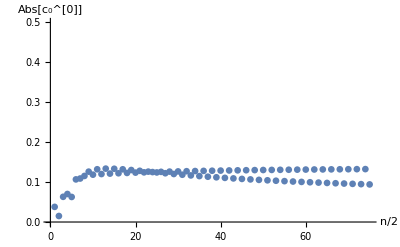

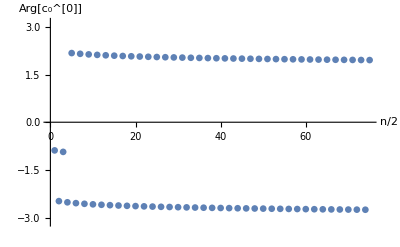

```mathematica
ps=0.012;
c00tabplotabs=ListPlot[Table[{n,c00tab[[n,1]]},{n,Length[c00tab]}],PlotRange->{{0,Length[c00tab]},{0.0,0.5}},AxesLabel->{"n/2","Abs[c_0^[0]]"},BaseStyle->Directive[FontSize->15],PlotStyle->{PointSize[ps]}]
c00tabplotangle=ListPlot[Table[{n,c00tab[[n,2]]},{n,Length[c00tab]}],PlotRange->{{0,Length[c00tab]},{-π,π}},AxesLabel->{"n/2","Arg[c_0^[0]]"},BaseStyle->Directive[FontSize->15],PlotStyle->{PointSize[ps]}]
```

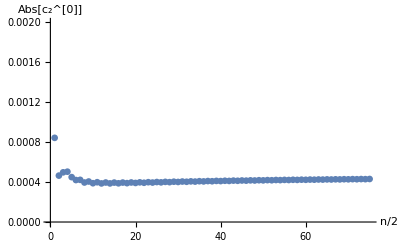

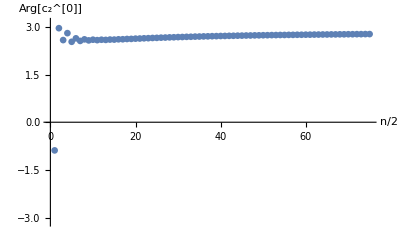

```mathematica
c20tabplotabs=ListPlot[Table[{n,c20tab[[n,1]]},{n,Length[c20tab]}],PlotRange->{{0,Length[c20tab]},{0,0.002}},AxesLabel->{"n/2","Abs[c_2^[0]]"},BaseStyle->Directive[FontSize->15],PlotStyle->{PointSize[ps]}]
c20tabplotangle=ListPlot[Table[{n,c20tab[[n,2]]},{n,Length[c20tab]}],PlotRange->{{0,Length[c20tab]},{-π,π}},AxesLabel->{"n/2","Arg[c_2^[0]]"},BaseStyle->Directive[FontSize->15],PlotStyle->{PointSize[ps]}]
```

{param_0→0.13864,param_1→-0.260132,param_2→1.28549}

{param_0→0.0637414,param_1→1.37657,param_2→-8.24212}

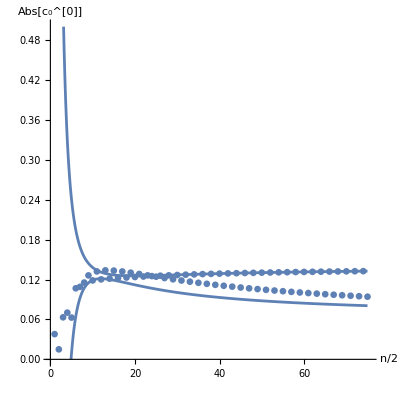

```mathematica
c00funabs=Subscript[param, 0]+Subscript[param, 1]/n+Subscript[param, 2]/n^2;
parameters={Subscript[param, 0],Subscript[param, 1],Subscript[param, 2]};
fitpar=FindFit[Table[{n,c00tab[[2*n,1]]},{n,20,Floor[Length[c00tab]/2]}],c00funabs,parameters,n]
fitplot1=Plot[c00funabs/.fitpar/.n->m/2,{m,0,Length[c00tab]},PlotRange->{{0,Length[c00tab]+0.5},{0,0.5}},BaseStyle->Directive[FontSize->15],AspectRatio->1];
fitpar=FindFit[Table[{n,c00tab[[2*n-1,1]]},{n,20,Floor[Length[c00tab]/2]}],c00funabs,parameters,n]
fitplot2=Plot[c00funabs/.fitpar/.n->m/2,{n,0,Length[c00tab]},PlotRange->{{0,Length[c00tab]+0.5},{0,0.5}},BaseStyle->Directive[FontSize->15],AspectRatio->1];
Show[fitplot1,fitplot2,c00tabplotabs,AxesLabel->{"n/2","Abs[c_0^[0]]"}]
```

{param_0→-2.84966,param_1→4.19334,param_2→-23.8258}

{param_0→1.86273,param_1→4.2392,param_2→-23.857}

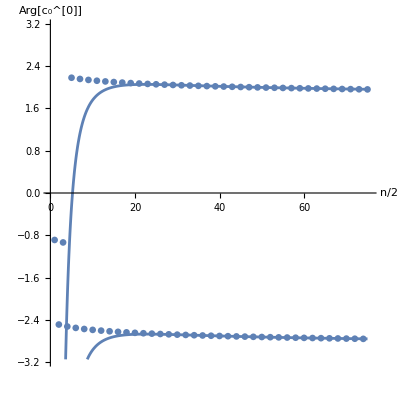

```mathematica
c00funangle=Subscript[param, 0]+Subscript[param, 1]/n+Subscript[param, 2]/n^2;
parameters={Subscript[param, 0],Subscript[param, 1],Subscript[param, 2]};
fitpar=FindFit[Table[{n,c00tab[[2*n,2]]},{n,15,Length[c00tab]/2}],c00funangle,parameters,n]
fitplot1=Plot[c00funangle/.fitpar/.n->m/2,{m,0,Length[c00tab]},PlotRange->{{0,Length[c00tab]+0.5},{-π,π}},BaseStyle->Directive[FontSize->15],AspectRatio->1];
fitpar=FindFit[Table[{n,c00tab[[2*n-1,2]]},{n,15,Length[c00tab]/2}],c00funangle,parameters,n]
fitplot2=Plot[c00funangle/.fitpar/.n->m/2,{m,0,Length[c00tab]},PlotRange->{{0,Length[c00tab]+0.5},{-π,π}},BaseStyle->Directive[FontSize->15],AspectRatio->1];
Show[fitplot1,fitplot2,c00tabplotangle,AxesLabel->{"n/2","Arg[c_0^[0]]"}]
```

{param_0→0.000456081,param_1→-0.00225914,param_2→0.020015}

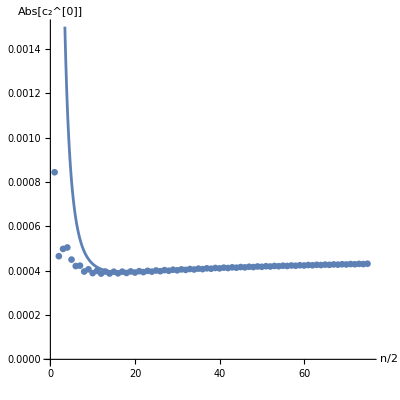

```mathematica
c20funabs=Subscript[param, 0]+Subscript[param, 1]/n+Subscript[param, 2]/n^2;
parameters={Subscript[param, 0],Subscript[param, 1],Subscript[param, 2]};
fitpar=FindFit[Table[{n,c20tab[[n,1]]},{n,15,Length[c20tab]}],c00funabs,parameters,n]
fitplot=Plot[c20funabs/.fitpar,{n,0,Length[c20tab]},PlotRange->{{0,Length[c20tab]+0.5},{0,0.0015}},AxesLabel->{"n/2","Abs[c_2^[0]]"},BaseStyle->Directive[FontSize->15],AspectRatio->1];
Show[fitplot,c20tabplotabs]
```

{param_0→2.8586,param_1→-6.94022,param_2→47.0781}

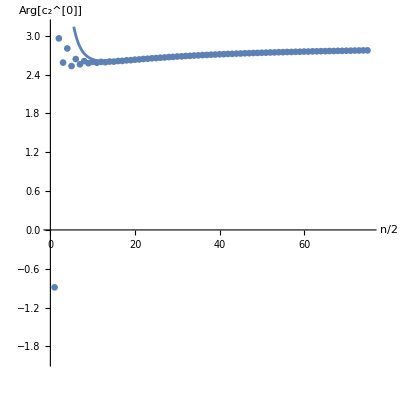

```mathematica
c20funangle=Subscript[param, 0]+Subscript[param, 1]/n+Subscript[param, 2]/n^2;
parameters={Subscript[param, 0],Subscript[param, 1],Subscript[param, 2]};
fitpar=FindFit[Table[{n,c20tab[[n,2]]},{n,15,Length[c20tab]}],c00funangle,parameters,n]
fitplot=Plot[c20funangle/.fitpar,{n,0,Length[c20tab]},PlotRange->{{0,Length[c20tab]+0.5},{-2,π}},AxesLabel->{"n/2","Arg[c_2^[0]]"},BaseStyle->Directive[FontSize->15],AspectRatio->1];
Show[fitplot,c20tabplotangle]
```